coursework part 1 - Time independent energy eigenvalues and transition matrix elements

```mathematica
symmetric2x2 = {{e0,v},{v,e1}};
symmetric2x2 // MatrixForm
ham = symmetric2x2 /. {e0 -> x, e1 -> 1, v->1/10};
ham // MatrixForm
evals = Eigenvalues[ham]
Plot[evals, {x,0,2}]
```

(e0 | v
v | e1)

(x | 1/10
1/10 | 1)

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

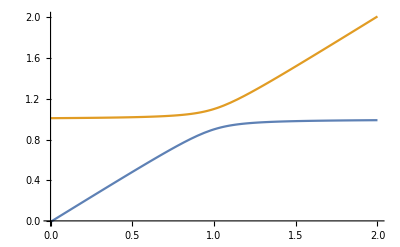

Exercise 1 : Basis state mixing

-Graphics-

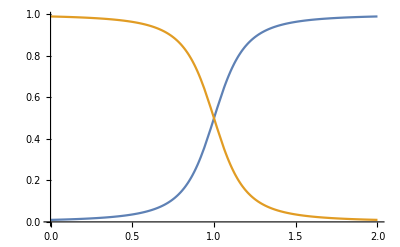

```mathematica
rules = {e0 -> x, e1 -> 1, v -> 1/10};
ham = symmetric2x2 /. rules;
evals = Eigenvalues[ham];
Plot[evals, {x,0,2}]
evecs := Eigenvectors[ham];
probl := Abs[Transpose[evecs][ [1] ]]^2;
Plot[probl, {x,0,2}]
```

Here,we have a two level system whose Hamiltonian is represented by a 2x2 matrix. Diagonal elements are the expectation energies of the two basis states that span the vector space of the two level system. V, the off-diagonal element,represents the overlap of the Hamiltonian between the 0 and 1 states. The variable x is used to vary the Hamiltonian. Which means that the pure state energies and the interaction energies are  functions of x. The two lines in the graph are the mean energy of the time independent Hamiltonian of the two level system. Initially the system is in the pure state 1 at x = 0 with energy equal to 1 and the probability for this state is 1 as well. As we increase x, that is when the energy difference between the two states decreases and the off-diagonal terms of overlapping states in the Hamiltonian matrix become dominant. Then, the probability of the basis states is equal to 0.5. However, when the energy difference is much larger, the contribution from the off diagonal mixed states become negligible and we get pure basis states. This means that the Hamiltonian will have only diagonal elements. As we can see in the graph, for larger values of x we get a pure state with probability 1. At x = 1, where the energy difference is lower than v, we get interacting basis states each with probability 0.5.

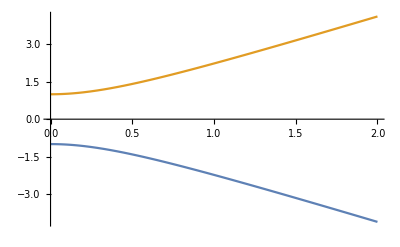

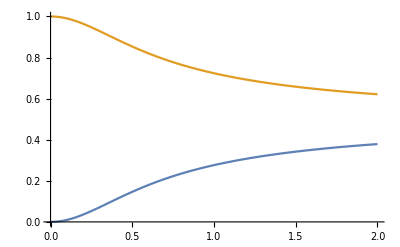

```mathematica
newrules= {e0 ->  1, e1 ->  -1, v -> 2x}; (*rules for pure eigenstates which approach mixed states*)
newham = symmetric2x2 /. newrules;
newevals = Eigenvalues[newham];
Plot[newevals, {x,0,2}]
newevecs := Eigenvectors[newham];
newprobl := Abs[Transpose[newevecs][ [1] ]]^2;
Plot[newprobl, {x,0,2}]
```

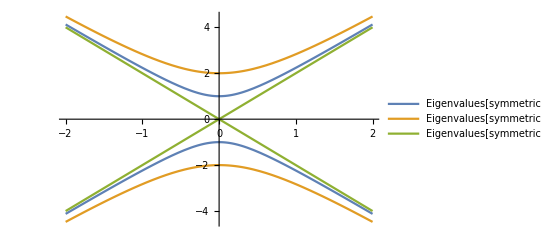

```mathematica
Plot[{Eigenvalues[symmetric2x2 /. {e0 -> 1, e1 -> -1, v -> 2x}], Eigenvalues[symmetric2x2 /. {e0 -> 2, e1 -> -2, v -> 2x}], Eigenvalues[symmetric2x2 /. {e0 -> 0, e1 -> 0, v -> 2x}]}, {x,-2,2}, PlotLegends-> "Expressions"]
```

Exercise 2 spin-spin interactions

```mathematica
echarge = 1.6 10^-19 (*in SI units C*)
emass = 9.1 10^-31 (*in SI units Kg*)
hbar = 1.05 10^-34 (*in SI units Js*)
bohrmagneton = (echarge hbar)/(2 emass) (*in SI units JsC/Kg = J/T*)
bohrmagneton = hbar/(2 emass)10^6(*μeV/T*)
```

57.6923

```mathematica
b0 = (2 5.87433(*μeV*))/(2 bohrmagneton(*μeV/T*))
```

0.101822

```mathematica
0.10182171999999996(*calculated value of b0 for Hydrogen*)
```

```mathematica
r = 2.793 1836.152
```

5128.37

```mathematica
`
```

```mathematica
ham2 =({{1/4-xminus, 0, 0, 0}, {0, -1/4-xplus, 1/2, 0}, {0, 1/2, -1/4+xplus, 0}, {0, 0, 0, 1/4+xminus}}) 
ham2 // MatrixForm
```

```mathematica
ham2 = ham2 /. {1/4-xminus -> 1/4-((1-r)b)/b0, -1/4-xplus ->-1/4- ((1+r)b)/b0, -1/4+xplus ->-1/4+ ((1+r)b)/b0,  1/4+xminus -> 1/4+((1-r)b)/b0}
```

{{1/4+50356.4 b,0,0,0},{0,-1/4-50376. b,1/2,0},{0,1/2,-1/4+50376. b,0},{0,0,0,1/4-50356.4 b}}

```mathematica
evals2 = Eigenvalues[ham2]
```

{-50356.4 (-4.96461×10^-6+1. b),50356.4 (4.96461×10^-6+1. b),1/2 (-0.5-√(1.+1.0151×10^10 b^2)),1/2 (-0.5+√(1.+1.0151×10^10 b^2))}

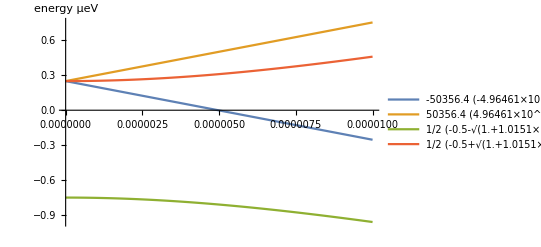

```mathematica
Plot[evals2, {b,0,0.00001}, AxesLabel-> energy (μeV), PlotLegends->"Expressions"]
```

Varying b0 and r does not change the graph. The energy eigenvalues are independent of the

#### Exercise 3: The Dirac equation

```mathematica
hamd =({{m, 0, kz, kx-ⅈ ky}, {0, m, kx+ⅈ ky, -kz}, {kz, kx-ⅈ ky, -m, 0}, {kx+ⅈ ky, -kz, 0, -m}})
```

{{m,0,kz,kx-ⅈ ky},{0,m,kx+ⅈ ky,-kz},{kz,kx-ⅈ ky,-m,0},{kx+ⅈ ky,-kz,0,-m}}

```mathematica
hamd // MatrixForm
hamd = hamd /. {kz -> k, kx -> 0,  Im[kx-ⅈ ky] ->  0, m -> 0}
evald = Eigenvalues[hamd]
Plot[{Eigenvalues[hamd /.{kz -> k, kx -> 0,  Im[kx-ⅈ ky] ->  0, m -> 0} ], Eigenvalues[hamd /. {kz -> k, kx -> 0,  Im[kx-ⅈ ky] ->  0, m -> 1} ], Eigenvalues[hamd /. {kz -> k, kx -> 0,  Im[kx-ⅈ ky] ->  0, m -> 2}]}, {k, 0,10}, PlotLegends->"Expressions", AxesLabel->energy]
```

(0 | 0 | k | 0
0 | 0 | 0 | -k
k | 0 | 0 | 0
0 | -k | 0 | 0)

{{0,0,k,0},{0,0,0,-k},{k,0,0,0},{0,-k,0,0}}

{-k,-k,k,k}

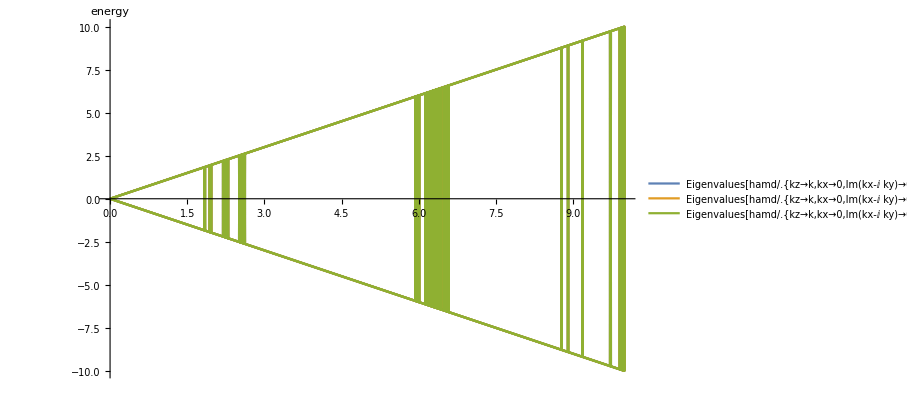

The slope at high energies is c which means ω = ck. The group velocity can exceed the speed of light if the values of k are close. However, information cannot be transmitted at this velocity because the changes that are required to be made to the plane waves in order for information to be transmitted cannot travel at a speed greater than light.

```mathematica
u = ({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})
u // MatrixForm;
udagger = ConjugateTranspose[u]// MatrixForm
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
udagger . u
```

```mathematica
({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}).{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}
```

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}} (*This verifies that u is a unitary matrix*)

udagger . hamd . u // MatrixForm
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}).{{0,k,0,0},{0,0,0,-k},{k,0,0,0},{0,0,-k,0}}
```

```mathematica
{{0,k,0,0},{k,0,0,0},{0,0,0,-k},{0,0,-k,0}}// MatrixForm
```

(0 | k | 0 | 0
k | 0 | 0 | 0
0 | 0 | 0 | -k
0 | 0 | -k | 0)

This matrix we get is a block diagonal matrix. In the upper left corner block, the diagonal elements are zero and the off diagonal elements are both equal to k. This means that only mixed states are present with positive energy k. In the bottom right block, again the pure states are absent and the mixed states have energy -k. Which means both the states, matter and antimatter, have equal probability of 0.5.

#### Exercise 4: Graphene Band Structure

```mathematica
eh = 2.8 (*in units of eV*)
a = 0.142 10^-9  (*in SI units of m*)
```

```mathematica
Hermitian2x2 = ({{0, v}, {Conjugate[v], 0}})
Hermitian2x2 // MatrixForm
hamg = Hermitian2x2 /. {v ->  (-eh Exp[-ⅈ kx a]) (1 + 2 Exp[3 ⅈ kx a/2] Cos[Sqrt[3] ky a/2])};
hamg // MatrixForm
eigeng = Re[Eigenvalues[hamg]]
```

{{0,v},{Conjugate[v],0}}

(0 | v
Conjugate[v] | 0)

(0 | -ⅇ^(-ⅈ a kx) eh (1+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky])
-ⅇ^(ⅈ Conjugate[a kx]) Conjugate[eh] (1+2 ⅇ^(-3/2 ⅈ Conjugate[a kx]) Cos[1/2 √3 Conjugate[a ky]]) | 0)

{-Re[ⅇ^(-ⅈ a kx+1/2 (ⅈ a kx+1/2 ⅈ Conjugate[a kx])-1/2 ⅈ Conjugate[a kx]) √eh √Conjugate[eh] √(ⅇ^(3/2 ⅈ Conjugate[a kx])+2 ⅇ^((3 ⅈ a kx)/2+3/2 ⅈ Conjugate[a kx]) Cos[1/2 √3 a ky]+2 Cos[1/2 √3 Conjugate[a ky]]+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky-1/2 √3 Conjugate[a ky]]+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky+1/2 √3 Conjugate[a ky]])],Re[ⅇ^(-ⅈ a kx+1/2 (ⅈ a kx+1/2 ⅈ Conjugate[a kx])-1/2 ⅈ Conjugate[a kx]) √eh √Conjugate[eh] √(ⅇ^(3/2 ⅈ Conjugate[a kx])+2 ⅇ^((3 ⅈ a kx)/2+3/2 ⅈ Conjugate[a kx]) Cos[1/2 √3 a ky]+2 Cos[1/2 √3 Conjugate[a ky]]+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky-1/2 √3 Conjugate[a ky]]+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky+1/2 √3 Conjugate[a ky]])]}

```mathematica
{-Re[ⅇ^(-ⅈ a kx) eh (1+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky])],Re[ⅇ^(-ⅈ a kx) eh (1+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky])]}
```

Plot3D::argrx: Plot3D called with 2 arguments; 3 arguments are expected.

```mathematica
e1 = Sqrt[3 +2 Cos[Sqrt[3] ky a]]+4 Cos[3 kx a/2] Cos[Sqrt[3] ky a/2]
a = 1;
Plot3D[{e1,-e1},{kx,-3,3},{ky,-3,3}, BoxRatios->{1, 1, 1}]
```

4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+√(3+2 Cos[√3 ky])

-Graphics3D-

#### Exercise 5: Transition Matrix elements

```mathematica
evals2 // List
```

{{-50356.4 (-4.96461×10^-6+1. b),50356.4 (4.96461×10^-6+1. b),1/2 (-0.5-√(1.+1.0151×10^10 b^2)),1/2 (-0.5+√(1.+1.0151×10^10 b^2))}}

Subtract::argr: Subtract called with 1 argument; 2 arguments are expected.

General::stop: Further output of Subtract::argr will be suppressed during this calculation.

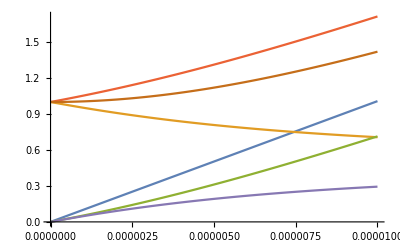

```mathematica
Plot[{Abs[Subtract[-50356.373237458596 (-4.96461488243225*^-6+1. b),50356.373237458596 (4.96461488243225*^-6+1. b)]], Abs[Subtract[-50356.373237458596 (-4.96461488243225*^-6+1. b),1/2 (-0.5-√(1.+1.0150971715174707*^10 b^2))]], Abs[Subtract[-50356.373237458596 (-4.96461488243225*^-6+1. b),1/2 (-0.5+√(1.+1.0150971715174707*^10 b^2))]], Abs[Subtract[50356.373237458596 (4.96461488243225*^-6+1. b),1/2 (-0.5-√(1.+1.0150971715174707*^10 b^2))]], Abs[Subtract[50356.373237458596 (4.96461488243225*^-6+1. b),1/2 (-0.5+√(1.+1.0150971715174707*^10 b^2))]],Abs[Subtract[1/2 (-0.5-√(1.+1.0150971715174707*^10 b^2)),1/2 (-0.5+√(1.+1.0150971715174707*^10 b^2))]]}, {b, 0, 0.00001}]
```

{{0,rs,1,0},{rs,0,0,1},{1,0,0,rs},{0,1,rs,0}}

(0 | rs | 1 | 0
rs | 0 | 0 | 1
1 | 0 | 0 | rs
0 | 1 | rs | 0)

{{-4-4 rs,0,0,0},{0,4-4 rs,0,0},{0,0,-4+4 rs,0},{0,0,0,4+4 rs}}

(-4-4 rs | 0 | 0 | 0
0 | 4-4 rs | 0 | 0
0 | 0 | -4+4 rs | 0
0 | 0 | 0 | 4+4 rs)

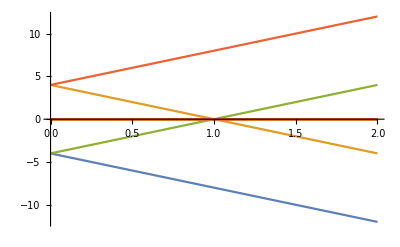

```mathematica
hamt = ({{0, rs, 1, 0}, {rs, 0, 0, 1}, {1, 0, 0, rs}, {0, 1, rs, 0}})
hamt // MatrixForm
c := Eigenvectors[hamt]
m = c†.hamt.c
m // MatrixForm
Plot[m, {rs,0,2}]
```